```mathematica
(* Clear cache *)
Clear["Global`*"]
(*1.Define generating function *)
(*1.1 Set these variables to simplify the expression of the final generating function*)
v=dm*w1-λ*w2-λ*w1*w2;
s=dm-λ*w2;
r=1+Sqrt[4*(ρ*σon*dm/s^3-ρ*σon/s^2)+(θ-2*σon/s)^2];
x=ρ*v/s^2;
θ=ρ*dm/s^2-(ρ+σoff-σon)/s;
k=1/2*(θ-2*σon/s+r-1);
ϵa=(r+θ-1)/2;
ϵb=(-r+θ+1)/2;
γa=Exp[ k*s*t-x*Exp[-s*t]]/(r-1);
γb=Exp[-s*t*(r-1)];
tw1=((dm*w1-λ*w2-λ*w1*w2)*Exp[-s*t]+λ*w2)/(dm-λ*w2);
k1[w1_,w2_,t_]=γa*(-ϵb*γb*Hypergeometric1F1[ϵa,r,x*Exp[-s*t]]*Hypergeometric1F1[ϵb+1,2-r,x]+ϵa*Hypergeometric1F1[ϵb,2-r,x*Exp[-s*t]]*Hypergeometric1F1[ϵa+1,r,x]);
k2[w1_,w2_,t_]=γa*σon/s*(-γb*Hypergeometric1F1[ϵa+1,r,x*Exp[-s*t]]*Hypergeometric1F1[ϵb+1,2-r,x]+Hypergeometric1F1[ϵb+1,2-r,x*Exp[-s*t]]*Hypergeometric1F1[ϵa+1,r,x]);
k3[w1_,w2_,t_]=γa*s*ϵa*ϵb/σon*(γb*Hypergeometric1F1[ϵa,r,x*Exp[-s*t]]*Hypergeometric1F1[ϵb,2-r,x]-Hypergeometric1F1[ϵb,2-r,x*Exp[-s*t]]*Hypergeometric1F1[ϵa,r,x]);
k4[w1_,w2_,t_]=γa*(ϵa*γb*Hypergeometric1F1[ϵa+1,r,x*Exp[-s*t]]*Hypergeometric1F1[ϵb,2-r,x]-ϵb*Hypergeometric1F1[ϵb+1,2-r,x*Exp[-s*t]]*Hypergeometric1F1[ϵa,r,x]);
(*1.2  Initial conditions: gene state is inactive, the number of mRNA is 6, the number of protein is 5*)
nm0=6;
np0=5;
g1[tw1_,w2_]=(tw1+1)^nm0*(w2+1)^np0;
g0[tw1_,w2_]=0;
(*1.3  Final generating function*)
G0=(k1[w1,w2,t]+k3[w1,w2,t])*g0[tw1,w2];
G1=(k2[w1,w2,t]+k4[w1,w2,t])*g1[tw1,w2];
```

```mathematica
(*2 Compared generating function solution with SSA*)
```

```mathematica
param={σoff->1,σon->1/10,ρ->1,λ->1,dm->1,t->1};
```

```mathematica
(*2.1 Plot SSA resuts*)
```

```mathematica
(*Import probability data from SSA*)
ssadata=Import["/Users/zhenhuayu/Desktop/CV_FF等7-3/t10.csv","Data"];
(*Plot SSA results*)
pssa=ListLinePlot[ssadata];
```

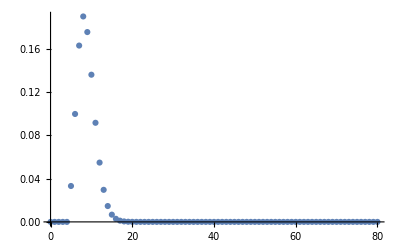

```mathematica
(*2.2 Plot exact solution*)
G=G0+G1/.param;
Bins=80;
(*For protein probability distribution,set w1->0;for mRNA probability distribution,set w2->0*)
Gp=G/.w1->0;
PP=ResourceFunction["NSeries"][Gp,{w2,-1,Bins}][[3]];
v=Table[{i-Bins-1,Re[PP[[i]]]},{i,Bins+1,2*Bins+1}];
pG=ListPlot[v,PlotRange->All]
```

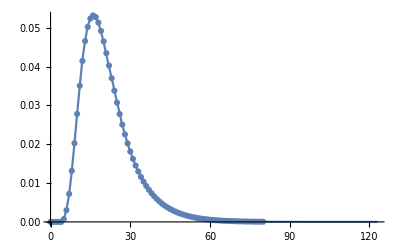

```mathematica
(*2.3 Show in a picture for a clearer comparison. Dot is the exact solution and line represents the SSA result*)
Show[pssa,pG]
```